```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### New code: EDSL-To-Trana-Notation

```mathematica
EDSLToTrana[{IndexedConcatenate[x__,iter0_]}]:=Module[{argList=List[x],basedArgList,k,LenArgList,iter,base},
iter=
Which[
AtomQ[iter0],{n,0,iter0-1},
Length[iter0]==2, {First[iter0],1,Last[iter0]},
True,iter0
];
If[$debug,Print["iter: ",iter]];
LenArgList= Length[argList];
If[$debug,Print["LenArgList: ",LenArgList]];
basedArgList=MapIndexed[{Expand[LenArgList * (iter[[1]]-iter[[2]])]+First[#2],#1}&,argList,{1}];
If[$debug,Print["argList: ",argList]];
If[$debug,Print["basedArgList: ",basedArgList]];
{IndexedConcatenate[
Sequence@@Flatten[
Replace[basedArgList, {base_,eds_List}:>(Rule[base,base+#]&/@eds),{1}]
],
iter]}
]
```

### Try it on ICN Paper Examples

#### Figure 5a

```mathematica
IC2a={IndexedConcatenate[{1},10]}
```

{€^10[{1}]}

```mathematica
EDSLToTrana[IC2a]
```

{€_(n⊨0)^9[1+n→2+n]}

```mathematica
Expand[%]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11}

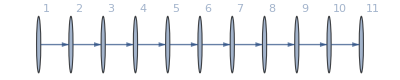

```mathematica
Graph[%,VertexLabels->Automatic]
```

```mathematica
{$debug=True,EDSLToTrana[IC2a],$debug=False}[[2]]
```

iter: {n,0,9}

LenArgList: 1

argList: {{1}}

basedArgList: {{1+n,{1}}}

{€_(n⊨0)^9[1+n→2+n]}

```mathematica
IC2a={IndexedConcatenate[{1},{n,1,10}]}
```

{€_(n⊨1)^10[{1}]}

```mathematica
EDSLToTrana[IC2a]
```

{€_(n⊨1)^10[n→1+n]}

```mathematica
Expand[%]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11}

```mathematica
Graph[%,VertexLabels->Automatic]
```

-Graphics-

```mathematica
{$debug=True,EDSLToTrana[IC2a],$debug=False}[[2]]
```

iter: {n,1,10}

kmax: 1

argList: {{1}}

basedArgList: {{n,{1}}}

{€_(n⊨1)^10[n→1+n]}

#### Figure 5b

```mathematica
IC2b={IndexedConcatenate[{1},{},{n,1,5}]}
```

{€_(n⊨1)^5[{1},{}]}

```mathematica
EDSLToTrana[IC2b]
```

{€_(n⊨1)^5[-1+2 n→2 n]}

```mathematica
Expand[%]
```

{1→2,3→4,5→6,7→8,9→10}

```mathematica
Graph[%,VertexLabels->Automatic]
```

-Graphics-

```mathematica
{$debug=True,EDSLToTrana[IC2b],$debug=False}[[2]]
```

iter: {n,1,5}

LenArgList: 2

argList: {{1},{}}

basedArgList: {{-1+2 n,{1}},{2 n,{}}}

{€_(n⊨1)^5[2 n-1→2 n]}

#### Figure 5c

```mathematica
IC2c={IndexedConcatenate[{1,2},{n,1,10}]}
```

{€_(n⊨1)^10[{1,2}]}

```mathematica
EDSLToTrana[%]
```

{€_(n⊨1)^10[n→n+1,n→n+2]}

```mathematica
Expand[%]
```

{1→2,1→3,2→3,2→4,3→4,3→5,4→5,4→6,5→6,5→7,6→7,6→8,7→8,7→9,8→9,8→10,9→10,9→11,10→11,10→12}

```mathematica
Graph[%,VertexLabels->Automatic]
```

-Graphics-

```mathematica
{$debug=True,EDSLToTrana[IC2c],$debug=False}[[2]]
```

iter: {n,1,10}

LenArgList: 1

argList: {{1,2}}

basedArgList: {{n,{1,2}}}

{€_(n⊨1)^10[n→n+1,n→n+2]}

#### Figure 6d

```mathematica
IC2d={IndexedConcatenate[{2,3},{3},{1,2},{m,1,9}]}
```

{€_(m⊨1)^9[{2,3},{3},{1,2}]}

```mathematica
EDSLToTrana[%]
```

{€_(m⊨1)^9[3 m-2→3 m,3 m-2→3 m+1,3 m-1→3 m+2,3 m→3 m+1,3 m→3 m+2]}

```mathematica
Expand[%]
```

{1→3,1→4,2→5,3→4,3→5,4→6,4→7,5→8,6→7,6→8,7→9,7→10,8→11,9→10,9→11,10→12,10→13,11→14,12→13,12→14,13→15,13→16,14→17,15→16,15→17,16→18,16→19,17→20,18→19,18→20,19→21,19→22,20→23,21→22,21→23,22→24,22→25,23→26,24→25,24→26,25→27,25→28,26→29,27→28,27→29}

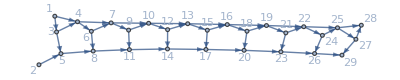

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
{$debug=True,EDSLToTrana[IC2d],$debug=False}[[2]]
```

iter: {m,1,9}

LenArgList: 3

argList: {{2,3},{3},{1,2}}

basedArgList: {{-2+3 m,{2,3}},{-1+3 m,{3}},{3 m,{1,2}}}

{€_(m⊨1)^9[3 m-2→3 m,3 m-2→3 m+1,3 m-1→3 m+2,3 m→3 m+1,3 m→3 m+2]}

```mathematica
IC2d0={IndexedConcatenate[{2,3},{3},{1,2},{m,0,8}]}
{$debug=True,EDSLToTrana[IC2d0],$debug=False}[[2]]
```

{€_(m⊨0)^8[{2,3},{3},{1,2}]}

iter: {m,0,8}

LenArgList: 3

argList: {{2,3},{3},{1,2}}

basedArgList: {{1+3 m,{2,3}},{2+3 m,{3}},{3+3 m,{1,2}}}

{€_(m⊨0)^8[3 m+1→3 m+3,3 m+1→3 m+4,3 m+2→3 m+5,3 m+3→3 m+4,3 m+3→3 m+5]}

#### Figure 5e

EDSL representations:

```mathematica
ICNB11={IndexedConcatenate[IndexedConcatenate[{2j-1, 2j}, {j, 1, 3}], IndexedConcatenate[{1, 2}, IndexedConcatenate[{}, 2], 2], 3]};
ICNB10={IndexedConcatenate[IndexedConcatenate[{2j+1, 2j+2}, {j,0,2}], IndexedConcatenate[{1, 2}, IndexedConcatenate[{}, {k,0,1}],{j,0,1}],{i,0,2}]};
Grid[{{ICNB11,Column[Partition[Expand[ICNB1],9]]},{ICNB10,SpanFromAbove}},Spacings->2,Alignment->{{Left,Left},{Center}}]
```

{€^3[€_(j⊨1)^3[{2 j-1,2 j}],€^2[{1,2},€^2[{}]]]} | {{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{}}
{{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{}}
{{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{}}
{€_(i⊨0)^2[€_(j⊨0)^2[{2 j+1,2 j+2}],€_(j⊨0)^1[{1,2},€_(k⊨0)^1[{}]]]} |

There are 9 edge difference sets in each row of the EDSL — for each “i” in the outer I-Cat, but they describe 10 edges, given below:

```mathematica
Grid[Riffle[#,","]& /@ Partition[FromNetDifferenceSets[ExpandAll[ICNB11]],10]]
```

1→2 | , | 1→3 | , | 2→5 | , | 2→6 | , | 3→8 | , | 3→9 | , | 4→5 | , | 4→6 | , | 7→8 | , | 7→9
10→11 | , | 10→12 | , | 11→14 | , | 11→15 | , | 12→17 | , | 12→18 | , | 13→14 | , | 13→15 | , | 16→17 | , | 16→18
19→20 | , | 19→21 | , | 20→23 | , | 20→24 | , | 21→26 | , | 21→27 | , | 22→23 | , | 22→24 | , | 25→26 | , | 25→27

The lengths of the internal ICs are 3×1=3, 2×(1+2×1)=6 , and 2×1=2.  The 9 comes from adding up the lengths of the ICs at the second level, that is, 3×1 + 2×(1+2×1)=3+2×3=3+6=9 elements

There is only 1 edge difference set inside the first “j” I-Cat, and 3 inside the second. In the following, 
(9i+j) comes from the 9 EDSs in the outer I-Cat and the 1 in the first “j” I-Cat;
(9i+3+3j) ”      ”        ”   9 EDSs  ”     ”       ”          ” ,   the 3 in order to to pass the first “j” I-Cat entirely, the 3j comes from the 3 EDSs in the 2nd “j” I-Cat. 
The final integer before each “→” is the vertex number in the inner I-Cat: 1.
The parenthesized expressions at the end of each “→” expression come from the EDSL internal expressions, when 0-indexed (2nd form shown above).

```mathematica
ICNB1TranaTemp=
{IndexedConcatenate[
IndexedConcatenate[Association[vertex->(9i+j)+1,EDS->{2 j+1,2 j+2}],{j,0,2}],
IndexedConcatenate[Association[vertex->(9i+3+3j)+1,EDS->{1,2}],{j,0,1}],
{i,0,2}
]}
```

```mathematica
ICNB1Trana=
{IndexedConcatenate[
IndexedConcatenate[(9i+j)+1->(9i+j)+1+(2j+1),(9i+j)+1->(9i+j)+1+(2j+2),{j,0,2}],
IndexedConcatenate[(9i+3+3j)+1->(9i+3+3j)+1+(1),(9i+3+3j)+1->(9i+3+3j)+1+(2),{j,0,1}],
{i,0,2}
]}
```

{€_(i⊨0)^2[€_(j⊨0)^2[1+9 i+j→2+9 i+3 j,1+9 i+j→3+9 i+3 j],€_(j⊨0)^1[4+9 i+3 j→5+9 i+3 j,4+9 i+3 j→6+9 i+3 j]]}

{€_(i⊨0)^2[€_(j⊨0)^2[(9i+j)+1->(9i+j)+1+(2j+1),(9i+j)+1->(9i+j)+1+(2j+2),],€_(j⊨0)^1[(9i+3+3j)+1->(9i+3+3j)+1+(1),(9i+3+3j)+1->(9i+3+3j)+1+(2)]]}

```mathematica
ExpandAll[ICNB1Trana]
```

{1→2,1→3,2→5,2→6,3→8,3→9,4→5,4→6,7→8,7→9,10→11,10→12,11→14,11→15,12→17,12→18,13→14,13→15,16→17,16→18,19→20,19→21,20→23,20→24,21→26,21→27,22→23,22→24,25→26,25→27}

```mathematica
FromNetDifferenceSets@ExpandAll[ICNB11]
```

{1→2,1→3,2→5,2→6,3→8,3→9,4→5,4→6,7→8,7→9,10→11,10→12,11→14,11→15,12→17,12→18,13→14,13→15,16→17,16→18,19→20,19→21,20→23,20→24,21→26,21→27,22→23,22→24,25→26,25→27}

```mathematica
%133==%134
```

True

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 5f

```mathematica
ICNB2={IndexedConcatenate[{2,2,2},{1,3,3},{2},{1,1,3},{2},{1,1,1},{3},4]}
```

{€^4[{2,2,2},{1,3,3},{2},{1,1,3},{2},{1,1,1},{3}]}

```mathematica
EDSLToTrana[%]
```

{€_(n⊨0)^3[1+7 n→3+7 n,1+7 n→3+7 n,1+7 n→3+7 n,2+7 n→3+7 n,2+7 n→5+7 n,2+7 n→5+7 n,3+7 n→5+7 n,4+7 n→5+7 n,4+7 n→5+7 n,4+7 n→7+7 n,5+7 n→7+7 n,6+7 n→7+7 n,6+7 n→7+7 n,6+7 n→7+7 n,7+7 n→10+7 n]}

```mathematica
Expand[%]
```

{1→3,1→3,1→3,2→3,2→5,2→5,3→5,4→5,4→5,4→7,5→7,6→7,6→7,6→7,7→10,8→10,8→10,8→10,9→10,9→12,9→12,10→12,11→12,11→12,11→14,12→14,13→14,13→14,13→14,14→17,15→17,15→17,15→17,16→17,16→19,16→19,17→19,18→19,18→19,18→21,19→21,20→21,20→21,20→21,21→24,22→24,22→24,22→24,23→24,23→26,23→26,24→26,25→26,25→26,25→28,26→28,27→28,27→28,27→28,28→31}

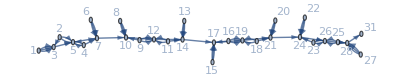

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 5g

```mathematica
ICNB3={IndexedConcatenate[{2, 3}, {1, 2}, {}, 8]}
```

{€^8[{2,3},{1,2},{}]}

```mathematica
EDSLToTrana[%]
```

{€_(n⊨0)^7[1+3 n→3+3 n,1+3 n→4+3 n,2+3 n→3+3 n,2+3 n→4+3 n]}

```mathematica
Expand[%]
```

{1→3,1→4,2→3,2→4,4→6,4→7,5→6,5→7,7→9,7→10,8→9,8→10,10→12,10→13,11→12,11→13,13→15,13→16,14→15,14→16,16→18,16→19,17→18,17→19,19→21,19→22,20→21,20→22,22→24,22→25,23→24,23→25}

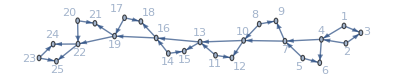

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 5h

```mathematica
ICNB4={IndexedConcatenate[{1, 6, 8}, {}, {IndexedConcatenate[2,4]}, IndexedConcatenate[{1, IndexedConcatenate[3,3]}, {}, 2], 7]}
```

{€^7[{1,6,8},{},{€^4[2]},€^2[{1,€^3[3]},{}]]}

```mathematica
EDSLToTrana[%]
```

{€_(n⊨0)^6[1+4 n→2+4 n,1+4 n→7+4 n,1+4 n→9+4 n,3+4 n→3+4 n+€^4[2],4+4 n,€^2[{1,€^3[3]},{}]]}

```mathematica
Expand[%]
```

{1→2,1→7,1→9,3→11,4,{1,3,3,3},{},{1,3,3,3},{},5→6,5→11,5→13,7→15,8,{1,3,3,3},{},{1,3,3,3},{},9→10,9→15,9→17,11→19,12,{1,3,3,3},{},{1,3,3,3},{},13→14,13→19,13→21,15→23,16,{1,3,3,3},{},{1,3,3,3},{},17→18,17→23,17→25,19→27,20,{1,3,3,3},{},{1,3,3,3},{},21→22,21→27,21→29,23→31,24,{1,3,3,3},{},{1,3,3,3},{},25→26,25→31,25→33,27→35,28,{1,3,3,3},{},{1,3,3,3},{}}

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

Graph[{1→2,1→7,1→9,3→11,4,{1,3,3,3},{},{1,3,3,3},{},5→6,5→11,5→13,7→15,8,{1,3,3,3},{},{1,3,3,3},{},9→10,9→15,9→17,11→19,12,{1,3,3,3},{},{1,3,3,3},{},13→14,13→19,13→21,15→23,16,{1,3,3,3},{},{1,3,3,3},{},17→18,17→23,17→25,19→27,20,{1,3,3,3},{},{1,3,3,3},{},21→22,21→27,21→29,23→31,24,{1,3,3,3},{},{1,3,3,3},{},25→26,25→31,25→33,27→35,28,{1,3,3,3},{},{1,3,3,3},{}},VertexLabels→Automatic,GraphLayout→SpringElectricalEmbedding]

#### Figure 5i

```mathematica
ICB5={IndexedConcatenate[IndexedConcatenate[{1,18-2k},{k,1,7}],IndexedConcatenate[{1,1},{k,8,9}],{n,0,25}]}
```

{€_(n⊨0)^25[€_(k⊨1)^7[{1,18-2 k}],€_(k⊨8)^9[{1,1}]]}

```mathematica
EDSLToTrana[%]
```

{€_(n⊨0)^25[1+2 n,€_(k⊨1)^7[{1,18-2 k}],2+2 n,€_(k⊨8)^9[{1,1}]]}

```mathematica
Expand[%]
```

{1,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},2,{1,1},{1,1},3,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},4,{1,1},{1,1},5,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},6,{1,1},{1,1},7,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},8,{1,1},{1,1},9,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},10,{1,1},{1,1},11,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},12,{1,1},{1,1},13,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},14,{1,1},{1,1},15,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},16,{1,1},{1,1},17,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},18,{1,1},{1,1},19,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},20,{1,1},{1,1},21,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},22,{1,1},{1,1},23,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},24,{1,1},{1,1},25,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},26,{1,1},{1,1},27,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},28,{1,1},{1,1},29,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},30,{1,1},{1,1},31,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},32,{1,1},{1,1},33,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},34,{1,1},{1,1},35,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},36,{1,1},{1,1},37,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},38,{1,1},{1,1},39,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},40,{1,1},{1,1},41,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},42,{1,1},{1,1},43,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},44,{1,1},{1,1},45,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},46,{1,1},{1,1},47,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},48,{1,1},{1,1},49,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},50,{1,1},{1,1},51,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},52,{1,1},{1,1}}

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

Graph[{1,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},2,{1,1},{1,1},3,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},4,{1,1},{1,1},5,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},6,{1,1},{1,1},7,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},8,{1,1},{1,1},9,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},10,{1,1},{1,1},11,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},12,{1,1},{1,1},13,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},14,{1,1},{1,1},15,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},16,{1,1},{1,1},17,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},18,{1,1},{1,1},19,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},20,{1,1},{1,1},21,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},22,{1,1},{1,1},23,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},24,{1,1},{1,1},25,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},26,{1,1},{1,1},27,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},28,{1,1},{1,1},29,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},30,{1,1},{1,1},31,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},32,{1,1},{1,1},33,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},34,{1,1},{1,1},35,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},36,{1,1},{1,1},37,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},38,{1,1},{1,1},39,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},40,{1,1},{1,1},41,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},42,{1,1},{1,1},43,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},44,{1,1},{1,1},45,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},46,{1,1},{1,1},47,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},48,{1,1},{1,1},49,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},50,{1,1},{1,1},51,{1,16},{1,14},{1,12},{1,10},{1,8},{1,6},{1,4},52,{1,1},{1,1}},VertexLabels→Automatic,GraphLayout→SpringElectricalEmbedding]

#### Figure 5j

```mathematica
ICB6={IndexedConcatenate[IndexedConcatenate[{1,7,8},2],IndexedConcatenate[{1,1,7},2],{7},{},{},13]}
```

{€^13[€^2[{1,7,8}],€^2[{1,1,7}],{7},{},{}]}

```mathematica
EDSLToTrana[%]
```

{€_(n⊨0)^12[1+5 n,€^2[{1,7,8}],2+5 n,€^2[{1,1,7}],3+5 n→10+5 n]}

```mathematica
Expand[%]
```

{1,{1,7,8},{1,7,8},2,{1,1,7},{1,1,7},3→10,6,{1,7,8},{1,7,8},7,{1,1,7},{1,1,7},8→15,11,{1,7,8},{1,7,8},12,{1,1,7},{1,1,7},13→20,16,{1,7,8},{1,7,8},17,{1,1,7},{1,1,7},18→25,21,{1,7,8},{1,7,8},22,{1,1,7},{1,1,7},23→30,26,{1,7,8},{1,7,8},27,{1,1,7},{1,1,7},28→35,31,{1,7,8},{1,7,8},32,{1,1,7},{1,1,7},33→40,36,{1,7,8},{1,7,8},37,{1,1,7},{1,1,7},38→45,41,{1,7,8},{1,7,8},42,{1,1,7},{1,1,7},43→50,46,{1,7,8},{1,7,8},47,{1,1,7},{1,1,7},48→55,51,{1,7,8},{1,7,8},52,{1,1,7},{1,1,7},53→60,56,{1,7,8},{1,7,8},57,{1,1,7},{1,1,7},58→65,61,{1,7,8},{1,7,8},62,{1,1,7},{1,1,7},63→70}

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

Graph[{1,{1,7,8},{1,7,8},2,{1,1,7},{1,1,7},3→10,6,{1,7,8},{1,7,8},7,{1,1,7},{1,1,7},8→15,11,{1,7,8},{1,7,8},12,{1,1,7},{1,1,7},13→20,16,{1,7,8},{1,7,8},17,{1,1,7},{1,1,7},18→25,21,{1,7,8},{1,7,8},22,{1,1,7},{1,1,7},23→30,26,{1,7,8},{1,7,8},27,{1,1,7},{1,1,7},28→35,31,{1,7,8},{1,7,8},32,{1,1,7},{1,1,7},33→40,36,{1,7,8},{1,7,8},37,{1,1,7},{1,1,7},38→45,41,{1,7,8},{1,7,8},42,{1,1,7},{1,1,7},43→50,46,{1,7,8},{1,7,8},47,{1,1,7},{1,1,7},48→55,51,{1,7,8},{1,7,8},52,{1,1,7},{1,1,7},53→60,56,{1,7,8},{1,7,8},57,{1,1,7},{1,1,7},58→65,61,{1,7,8},{1,7,8},62,{1,1,7},{1,1,7},63→70},VertexLabels→Automatic,GraphLayout→SpringElectricalEmbedding]

#### Figure 5k

```mathematica
ICB5b={IndexedConcatenate[IndexedConcatenate[{1,12-2k},{k,1,4}],IndexedConcatenate[{1,1},{k,5,7}],{n,0,18}]}
```

{€_(n⊨0)^18[€_(k⊨1)^4[{1,12-2 k}],€_(k⊨5)^7[{1,1}]]}

```mathematica
EDSLToTrana[%]
```

{€_(n⊨0)^18[1+2 n,€_(k⊨1)^4[{1,12-2 k}],2+2 n,€_(k⊨5)^7[{1,1}]]}

```mathematica
Expand[%]
```

{1,{1,10},{1,8},{1,6},{1,4},2,{1,1},{1,1},{1,1},3,{1,10},{1,8},{1,6},{1,4},4,{1,1},{1,1},{1,1},5,{1,10},{1,8},{1,6},{1,4},6,{1,1},{1,1},{1,1},7,{1,10},{1,8},{1,6},{1,4},8,{1,1},{1,1},{1,1},9,{1,10},{1,8},{1,6},{1,4},10,{1,1},{1,1},{1,1},11,{1,10},{1,8},{1,6},{1,4},12,{1,1},{1,1},{1,1},13,{1,10},{1,8},{1,6},{1,4},14,{1,1},{1,1},{1,1},15,{1,10},{1,8},{1,6},{1,4},16,{1,1},{1,1},{1,1},17,{1,10},{1,8},{1,6},{1,4},18,{1,1},{1,1},{1,1},19,{1,10},{1,8},{1,6},{1,4},20,{1,1},{1,1},{1,1},21,{1,10},{1,8},{1,6},{1,4},22,{1,1},{1,1},{1,1},23,{1,10},{1,8},{1,6},{1,4},24,{1,1},{1,1},{1,1},25,{1,10},{1,8},{1,6},{1,4},26,{1,1},{1,1},{1,1},27,{1,10},{1,8},{1,6},{1,4},28,{1,1},{1,1},{1,1},29,{1,10},{1,8},{1,6},{1,4},30,{1,1},{1,1},{1,1},31,{1,10},{1,8},{1,6},{1,4},32,{1,1},{1,1},{1,1},33,{1,10},{1,8},{1,6},{1,4},34,{1,1},{1,1},{1,1},35,{1,10},{1,8},{1,6},{1,4},36,{1,1},{1,1},{1,1},37,{1,10},{1,8},{1,6},{1,4},38,{1,1},{1,1},{1,1}}

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

Graph[{1,{1,10},{1,8},{1,6},{1,4},2,{1,1},{1,1},{1,1},3,{1,10},{1,8},{1,6},{1,4},4,{1,1},{1,1},{1,1},5,{1,10},{1,8},{1,6},{1,4},6,{1,1},{1,1},{1,1},7,{1,10},{1,8},{1,6},{1,4},8,{1,1},{1,1},{1,1},9,{1,10},{1,8},{1,6},{1,4},10,{1,1},{1,1},{1,1},11,{1,10},{1,8},{1,6},{1,4},12,{1,1},{1,1},{1,1},13,{1,10},{1,8},{1,6},{1,4},14,{1,1},{1,1},{1,1},15,{1,10},{1,8},{1,6},{1,4},16,{1,1},{1,1},{1,1},17,{1,10},{1,8},{1,6},{1,4},18,{1,1},{1,1},{1,1},19,{1,10},{1,8},{1,6},{1,4},20,{1,1},{1,1},{1,1},21,{1,10},{1,8},{1,6},{1,4},22,{1,1},{1,1},{1,1},23,{1,10},{1,8},{1,6},{1,4},24,{1,1},{1,1},{1,1},25,{1,10},{1,8},{1,6},{1,4},26,{1,1},{1,1},{1,1},27,{1,10},{1,8},{1,6},{1,4},28,{1,1},{1,1},{1,1},29,{1,10},{1,8},{1,6},{1,4},30,{1,1},{1,1},{1,1},31,{1,10},{1,8},{1,6},{1,4},32,{1,1},{1,1},{1,1},33,{1,10},{1,8},{1,6},{1,4},34,{1,1},{1,1},{1,1},35,{1,10},{1,8},{1,6},{1,4},36,{1,1},{1,1},{1,1},37,{1,10},{1,8},{1,6},{1,4},38,{1,1},{1,1},{1,1}},VertexLabels→Automatic,GraphLayout→SpringElectricalEmbedding]

#### Figure 6a

```mathematica
IC2D1={IndexedConcatenate[{1,1,1},{1,1,1+i},IndexedConcatenate[{1,1,2+i},-1+i],{2+i,3+i},{i,1,10}]}
```

{€_(i⊨1)^10[{1,1,1},{1,1,1+i},€^(-1+i)[{1,1,2+i}],{2+i,3+i}]}

```mathematica
EDSLToTrana[%]
```

{€_(i⊨1)^10[-3+4 i→-2+4 i,-3+4 i→-2+4 i,-3+4 i→-2+4 i,-2+4 i→-1+4 i,-2+4 i→-1+4 i,-2+4 i→-1+5 i,-1+4 i,€^(-1+i)[{1,1,2+i}],4 i→2+5 i,4 i→3+5 i]}

```mathematica
Expand[%]
```

{1→2,1→2,1→2,2→3,2→3,2→4,3,€^0[{1,1,3}],4→7,4→8,5→6,5→6,5→6,6→7,6→7,6→9,7,€^1[{1,1,4}],8→12,8→13,9→10,9→10,9→10,10→11,10→11,10→14,11,€^2[{1,1,5}],12→17,12→18,13→14,13→14,13→14,14→15,14→15,14→19,15,€^3[{1,1,6}],16→22,16→23,17→18,17→18,17→18,18→19,18→19,18→24,19,€^4[{1,1,7}],20→27,20→28,21→22,21→22,21→22,22→23,22→23,22→29,23,€^5[{1,1,8}],24→32,24→33,25→26,25→26,25→26,26→27,26→27,26→34,27,€^6[{1,1,9}],28→37,28→38,29→30,29→30,29→30,30→31,30→31,30→39,31,€^7[{1,1,10}],32→42,32→43,33→34,33→34,33→34,34→35,34→35,34→44,35,€^8[{1,1,11}],36→47,36→48,37→38,37→38,37→38,38→39,38→39,38→49,39,€^9[{1,1,12}],40→52,40→53}

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

Graph[{1→2,1→2,1→2,2→3,2→3,2→4,3,€^0[{1,1,3}],4→7,4→8,5→6,5→6,5→6,6→7,6→7,6→9,7,€^1[{1,1,4}],8→12,8→13,9→10,9→10,9→10,10→11,10→11,10→14,11,€^2[{1,1,5}],12→17,12→18,13→14,13→14,13→14,14→15,14→15,14→19,15,€^3[{1,1,6}],16→22,16→23,17→18,17→18,17→18,18→19,18→19,18→24,19,€^4[{1,1,7}],20→27,20→28,21→22,21→22,21→22,22→23,22→23,22→29,23,€^5[{1,1,8}],24→32,24→33,25→26,25→26,25→26,26→27,26→27,26→34,27,€^6[{1,1,9}],28→37,28→38,29→30,29→30,29→30,30→31,30→31,30→39,31,€^7[{1,1,10}],32→42,32→43,33→34,33→34,33→34,34→35,34→35,34→44,35,€^8[{1,1,11}],36→47,36→48,37→38,37→38,37→38,38→39,38→39,38→49,39,€^9[{1,1,12}],40→52,40→53},VertexLabels→Automatic,GraphLayout→SpringElectricalEmbedding]

#### Figure 6b

```mathematica
IC2D2={IndexedConcatenate[{-1+2 k,1+2 k},IndexedConcatenate[{1,1},{1,2 k},k],{k,1,12}]}
```

{€_(k⊨1)^12[{-1+2 k,1+2 k},€^k[{1,1},{1,2 k}]]}

```mathematica
EDSLToTrana[%]
```

{€_(k⊨1)^12[-1+2 k→-2+4 k,-1+2 k→4 k,2 k,€^k[{1,1},{1,2 k}]]}

```mathematica
Expand[%]
```

{1→2,1→4,2,€^1[{1,1},{1,2}],3→6,3→8,4,€^2[{1,1},{1,4}],5→10,5→12,6,€^3[{1,1},{1,6}],7→14,7→16,8,€^4[{1,1},{1,8}],9→18,9→20,10,€^5[{1,1},{1,10}],11→22,11→24,12,€^6[{1,1},{1,12}],13→26,13→28,14,€^7[{1,1},{1,14}],15→30,15→32,16,€^8[{1,1},{1,16}],17→34,17→36,18,€^9[{1,1},{1,18}],19→38,19→40,20,€^10[{1,1},{1,20}],21→42,21→44,22,€^11[{1,1},{1,22}],23→46,23→48,24,€^12[{1,1},{1,24}]}

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

Graph[{1→2,1→4,2,€^1[{1,1},{1,2}],3→6,3→8,4,€^2[{1,1},{1,4}],5→10,5→12,6,€^3[{1,1},{1,6}],7→14,7→16,8,€^4[{1,1},{1,8}],9→18,9→20,10,€^5[{1,1},{1,10}],11→22,11→24,12,€^6[{1,1},{1,12}],13→26,13→28,14,€^7[{1,1},{1,14}],15→30,15→32,16,€^8[{1,1},{1,16}],17→34,17→36,18,€^9[{1,1},{1,18}],19→38,19→40,20,€^10[{1,1},{1,20}],21→42,21→44,22,€^11[{1,1},{1,22}],23→46,23→48,24,€^12[{1,1},{1,24}]},VertexLabels→Automatic,GraphLayout→SpringElectricalEmbedding]

#### Figure 6c

```mathematica
IC2D4={IndexedConcatenate[IndexedConcatenate[{},{1,1,2,2k},k-1],{},{2k,2(1+k)},{k,1,8}]}
```

{€_(k⊨1)^8[€^(-1+k)[{},{1,1,2,2 k}],{},{2 k,2 (1+k)}]}

```mathematica
EDSLToTrana[%]
```

{€_(k⊨1)^8[-2+3 k,€^(-1+k)[{},{1,1,2,2 k}],3 k→5 k,3 k→3 k+2 (1+k)]}

```mathematica
Expand[%]
```

{1,€^0[{},{1,1,2,2}],3→5,3→7,4,€^1[{},{1,1,2,4}],6→10,6→12,7,€^2[{},{1,1,2,6}],9→15,9→17,10,€^3[{},{1,1,2,8}],12→20,12→22,13,€^4[{},{1,1,2,10}],15→25,15→27,16,€^5[{},{1,1,2,12}],18→30,18→32,19,€^6[{},{1,1,2,14}],21→35,21→37,22,€^7[{},{1,1,2,16}],24→40,24→42}

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

Graph[{1,€^0[{},{1,1,2,2}],3→5,3→7,4,€^1[{},{1,1,2,4}],6→10,6→12,7,€^2[{},{1,1,2,6}],9→15,9→17,10,€^3[{},{1,1,2,8}],12→20,12→22,13,€^4[{},{1,1,2,10}],15→25,15→27,16,€^5[{},{1,1,2,12}],18→30,18→32,19,€^6[{},{1,1,2,14}],21→35,21→37,22,€^7[{},{1,1,2,16}],24→40,24→42},VertexLabels→Automatic,GraphLayout→SpringElectricalEmbedding]

#### Figure 6d

```mathematica
IC3D1={IndexedConcatenate[IndexedConcatenate[IndexedConcatenate[HoldForm@{z=n(n+1)/2,z+i,z+i+1},i],{i,1,n}],{n,1,5}]}
```

{€_(n⊨1)^5[€_(i⊨1)^n[€^i[{z=1/2 n (n+1),z+i,z+i+1}]]]}

```mathematica
EDSLToTrana[%]
```

{€_(n⊨1)^5[n,€_(i⊨1)^n[€^i[{z=1/2 n (n+1),z+i,z+i+1}]]]}

```mathematica
Expand[%]
```

{1,€_(i⊨1)^1[€^i[{z=1/2 n (n+1),z+i,z+i+1}]],2,€_(i⊨1)^2[€^i[{z=1/2 n (n+1),z+i,z+i+1}]],3,€_(i⊨1)^3[€^i[{z=1/2 n (n+1),z+i,z+i+1}]],4,€_(i⊨1)^4[€^i[{z=1/2 n (n+1),z+i,z+i+1}]],5,€_(i⊨1)^5[€^i[{z=1/2 n (n+1),z+i,z+i+1}]]}

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

Graph[{1,€_(i⊨1)^1[€^i[{z=1/2 n (n+1),z+i,z+i+1}]],2,€_(i⊨1)^2[€^i[{z=1/2 n (n+1),z+i,z+i+1}]],3,€_(i⊨1)^3[€^i[{z=1/2 n (n+1),z+i,z+i+1}]],4,€_(i⊨1)^4[€^i[{z=1/2 n (n+1),z+i,z+i+1}]],5,€_(i⊨1)^5[€^i[{z=1/2 n (n+1),z+i,z+i+1}]]},VertexLabels→Automatic,GraphLayout→SpringElectricalEmbedding]

#### Figure 6e

```mathematica
IC2c={IndexedConcatenate[IndexedConcatenate[{k,k+1},k],{k,1,9}]}
```

{€_(k⊨1)^9[€^k[{k,1+k}]]}

```mathematica
EDSLToTrana[%]
```

{€_(k⊨1)^9[k,€^k[{k,1+k}]]}

```mathematica
Expand[%]
```

{1,€^1[{1,2}],2,€^2[{2,3}],3,€^3[{3,4}],4,€^4[{4,5}],5,€^5[{5,6}],6,€^6[{6,7}],7,€^7[{7,8}],8,€^8[{8,9}],9,€^9[{9,10}]}

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

Graph[{1,€^1[{1,2}],2,€^2[{2,3}],3,€^3[{3,4}],4,€^4[{4,5}],5,€^5[{5,6}],6,€^6[{6,7}],7,€^7[{7,8}],8,€^8[{8,9}],9,€^9[{9,10}]},VertexLabels→Automatic,GraphLayout→SpringElectricalEmbedding]

#### Figure 6f

```mathematica
IC2j={IndexedConcatenate[{-1 + 2^k, 2^k, 1 + 2^k}, IndexedConcatenate[{1 + 2^k}, 1 + 2^k], {1}, 
 IndexedConcatenate[{1, -1 + 2^k + j, 2^k + j}, {j, 1, -1 + 2^k}], {k, 1, 10}]}
```

{€_(k⊨1)^10[{-1+2^k,2^k,1+2^k},€^(1+2^k)[{1+2^k}],{1},€_(j⊨1)^(-1+2^k)[{1,-1+2^k+j,2^k+j}]]}

```mathematica
EDSLToTrana[%]
```

{€_(k⊨1)^10[-3+4 k→-4+2^k+4 k,-3+4 k→-3+2^k+4 k,-3+4 k→-2+2^k+4 k,-2+4 k,€^(1+2^k)[{1+2^k}],-1+4 k→4 k,4 k,€_(j⊨1)^(-1+2^k)[{1,-1+2^k+j,2^k+j}]]}

```mathematica
Expand[%]
```

{1→2,1→3,1→4,2,€^3[{3}],3→4,4,€_(j⊨1)^1[{1,1+j,2+j}],5→8,5→9,5→10,6,€^5[{5}],7→8,8,€_(j⊨1)^3[{1,3+j,4+j}],9→16,9→17,9→18,10,€^9[{9}],11→12,12,€_(j⊨1)^7[{1,7+j,8+j}],13→28,13→29,13→30,14,€^17[{17}],15→16,16,€_(j⊨1)^15[{1,15+j,16+j}],17→48,17→49,17→50,18,€^33[{33}],19→20,20,€_(j⊨1)^31[{1,31+j,32+j}],21→84,21→85,21→86,22,€^65[{65}],23→24,24,€_(j⊨1)^63[{1,63+j,64+j}],25→152,25→153,25→154,26,€^129[{129}],27→28,28,€_(j⊨1)^127[{1,127+j,128+j}],29→284,29→285,29→286,30,€^257[{257}],31→32,32,€_(j⊨1)^255[{1,255+j,256+j}],33→544,33→545,33→546,34,€^513[{513}],35→36,36,€_(j⊨1)^511[{1,511+j,512+j}],37→1060,37→1061,37→1062,38,€^1025[{1025}],39→40,40,€_(j⊨1)^1023[{1,1023+j,1024+j}]}

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Graph[{1->2,1->3,1->4,2,€^3[{3}],3->4,4,€_(j⊨1)^1[{1,1+j,2+j}],5->8,5->9,5->10,6,€^5[{5}],7->8,8,€_(j⊨1)^3[{1,3+j,4+j}],9->16,9->17,9->18,10,€^9[{9}],11->12,12,€_(j⊨1)^7[{1,7+j,8+j}],13->28,13->29,13->30,14,€^17[{17}],15->16,16,€_(j⊨1)^15[{1,15+j,16+j}],17->48,17->49,17->50,18,€^33[{33}],19->20,20,€_(j⊨1)^31[{1,31+j,32+j}],21->84,21->85,21->86,22,€^65[{65}],23->24,24,€_(j⊨1)^63[{1,63+j,64+j}],25->152,25->153,25->154,26,€^129[{129}],27->28,28,€_(j⊨1)^127[{1,127+j,128+j}],29->284,29->285,29->286,30,€^257[{257}],31->32,32,€_(j⊨1)^255[{1,255+j,256+j}],33->544,33->545,33->546,34,€^513[{513}],35->36,36,€_(j⊨1)^511[{1,511+j,512+j}],37->1060,37->1061,37->1062,38,€^1025[{1025}],39->40,40,€_(j⊨1)^1023[{1,1023+j,1024+j}]},VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```